## TissueCells-example.nb TissueCells, TissueEdges, TissueVertices

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51h (15 June 2017)) loaded Sun 18 Jun 2017 09:47:45
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

There are 8 cells in the tissue.

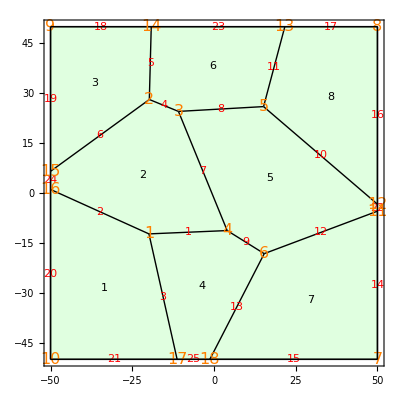

```mathematica
q=TemplateRandomSquareGrid[9, {-50, -50}, {50, 50}];
Print["There are ", NTissueCells[q], " cells in the tissue."];  
ShowTissue[q, "CellNumbers"-> True, Frame-> True, "EdgeNumbers"-> True, "EdgeNumberStyle"-> {Red, Background-> Yellow}, "VertexNumbers"-> True, "VertexNumberStyle"-> {Orange, FontSize-> 16}]
```

```mathematica
q
```

Tissue[{{-19.8977,-12.2927},{-19.7825,28.1031},{-10.8709,24.5241},{4.03225,-11.2907},{15.1608,25.9709},{15.3584,-18.2318},{50,-50},{50,50},{-50,50},{-50,-50},{50.,-5.45741},{50.,-3.36423},{21.6677,50.},{-19.1951,50.},{-50.,6.51783},{-50.,1.07214},{-11.2825,-50.},{-1.27506,-50.}},{{1,4},{1,16},{1,17},{2,3},{2,14},{2,15},{3,4},{3,5},{4,6},{5,12},{5,13},{6,11},{6,18},{7,11},{7,18},{8,12},{8,13},{9,14},{9,15},{10,16},{10,17},{11,12},{13,14},{15,16},{17,18}},{{21,3,2,20},{24,2,1,7,4,6},{19,6,5,18},{25,13,9,1,3},{22,10,8,7,9,12},{23,5,4,8,11},{12,13,15,14},{17,11,10,16}}]

```mathematica
TissueVertices[q]
```

{{-19.8977,-12.2927},{-19.7825,28.1031},{-10.8709,24.5241},{4.03225,-11.2907},{15.1608,25.9709},{15.3584,-18.2318},{50,-50},{50,50},{-50,50},{-50,-50},{50.,-5.45741},{50.,-3.36423},{21.6677,50.},{-19.1951,50.},{-50.,6.51783},{-50.,1.07214},{-11.2825,-50.},{-1.27506,-50.}}

```mathematica
TissueEdges[q]
```

{{1,4},{1,16},{1,17},{2,3},{2,14},{2,15},{3,4},{3,5},{4,6},{5,12},{5,13},{6,11},{6,18},{7,11},{7,18},{8,12},{8,13},{9,14},{9,15},{10,16},{10,17},{11,12},{13,14},{15,16},{17,18}}

```mathematica
TissueCells[q]
```

{{21,3,2,20},{24,2,1,7,4,6},{19,6,5,18},{25,13,9,1,3},{22,10,8,7,9,12},{23,5,4,8,11},{12,13,15,14},{17,11,10,16}}